# Binomial Distribution

Number of Attempts:

```mathematica
InputField[Dynamic[n]]
```

Probability of Success:

```mathematica
InputField[Dynamic[p]]
```

Plot!

Plot!

Print Distribution List

Print Distribution List

{4.14952×10^-20,2.07476×10^-18,5.16096×10^-17,8.51558×10^-16,1.04848×10^-14,1.02751×10^-13,8.34853×10^-13,5.78434×10^-12,3.48868×10^-11,1.86063×10^-10,8.88451×10^-10,3.83649×10^-9,1.51062×10^-8,5.46147×10^-8,1.82374×10^-7,5.65359×10^-7,1.63424×10^-6,4.42207×10^-6,0.0000112394,0.0000269154,0.0000608962,0.000130492,0.000265432,0.000513554,0.000946865,0.00166648,0.00280418,0.00451784,0.00697845,0.0103474,0.014745,0.0202149,0.02669,0.0339691,0.041712,0.0494585,0.0566712,0.0627978,0.0673424,0.0699325,0.0703696,0.0686533,0.0649754,0.0596867,0.0532433,0.0461442,0.0388714,0.0318415,0.0253737,0.0196776,0.0148566,0.0109239,0.00782532,0.00546296,0.00371785,0.0024673,0.00159714,0.00100872,0.000621752,0.000374105,0.000219787,0.000126107,0.0000706811,0.0000387063,0.0000207139,0.000010835,5.54061×10^-6,2.77031×10^-6,1.3546×10^-6,6.47851×10^-7,3.03102×10^-7,1.38744×10^-7,6.21456×10^-8,2.72419×10^-8,1.16883×10^-8,4.90907×10^-9,2.01853×10^-9,8.12656×10^-10,3.20374×10^-10,1.23689×10^-10,4.67698×10^-11,1.73221×10^-11,6.28455×10^-12,2.23367×10^-12,7.77795×10^-13,2.65365×10^-13,8.87122×10^-14,2.90609×10^-14,9.32921×10^-15,2.93503×10^-15,9.04968×10^-16,2.73479×10^-16,8.10034×10^-17,2.35171×10^-17,6.69237×10^-18,1.86682×10^-18,5.10459×10^-19,1.36824×10^-19,3.59512×10^-20,9.26015×10^-21,2.33819×10^-21,5.7876×10^-22,1.40434×10^-22,3.34043×10^-23,7.78898×10^-24,1.78034×10^-24,3.98896×10^-25,8.76081×10^-26,1.88601×10^-26,3.97965×10^-27,8.23064×10^-28,1.66837×10^-28,3.3144×10^-29,6.45282×10^-30,1.23113×10^-30,2.30168×10^-31,4.21643×10^-32,7.56796×10^-33,1.33081×10^-33,2.29257×10^-34,3.8687×10^-35,6.39455×10^-36,1.03518×10^-36,1.64114×10^-37,2.54774×10^-38,3.87257×10^-39,5.76276×10^-40,8.39457×10^-41,1.19688×10^-41,1.67007×10^-42,2.28028×10^-43,3.04618×10^-44,3.9808×10^-45,5.08825×10^-46,6.36031×10^-47,7.77371×10^-48,9.28844×10^-49,1.08478×10^-49,1.23807×10^-50,1.38058×10^-51,1.50384×10^-52,1.59983×10^-53,1.6618×10^-54,1.68504×10^-55,1.66749×10^-56,1.60999×10^-57,1.51626×10^-58,1.39248×10^-59,1.24665×10^-60,1.08768×10^-61,9.24526×10^-63,7.65336×10^-64,6.168×10^-65,4.83765×10^-66,3.69106×10^-67,2.73853×10^-68,1.9749×10^-69,1.38369×10^-70,9.41434×10^-72,6.21702×10^-73,3.98278×10^-74,2.47378×10^-75,1.48885×10^-76,8.67732×10^-78,4.89422×10^-79,2.66958×10^-80,1.40716×10^-81,7.16217×10^-83,3.51714×10^-84,1.66492×10^-85,7.59006×10^-87,3.32898×10^-88,1.4032×10^-89,5.6777×10^-91,2.20255×10^-92,8.18092×10^-94,2.90515×10^-95,9.84798×10^-97,3.18123×10^-98,9.77473×10^-100,2.85096×10^-101,7.87559×10^-103,2.05544×10^-104,5.05437×10^-106,1.16745×10^-107,2.52421×10^-109,5.08914×10^-111,9.52513×10^-113,1.64663×10^-114,2.6137×10^-116,3.78299×10^-118,4.95155×10^-120,5.8026×10^-122,6.01306×10^-124,5.42415×10^-126,4.17242×10^-128,2.66098×10^-130,1.35075×10^-132,5.11649×10^-135,1.28555×10^-137,1.60694×10^-140}

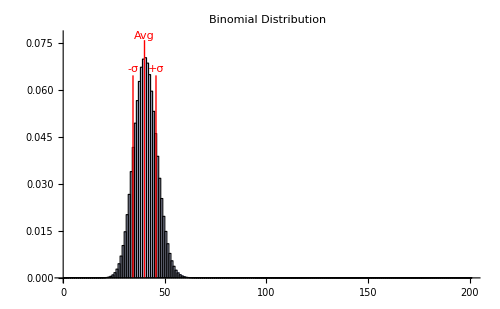

Avg=40.

σ=5.65685

```mathematica
L=Lo=N[n!/((0!)*(n-0)!)*(p)^0(1-(p))^(n-0)];
Binom=Prepend[Freq=Table[L=(n-j)/(j+1)*((p)/(1-(p)))*L,{j,0,n-1}],Lo];
Stddev=N[Sqrt[(n*p)*(1-p)]];
avg=N[n*p];
Needs["Histograms`"];
Show[Histogram[Binom,FrequencyData->True],Graphics[{RGBColor[1,0,0],Line[{{avg,0},{avg,Max[Binom]+.08Max[Binom]}}],Text["Avg",{avg,Max[Binom]+.1Max[Binom]}],{Line[{{avg+Stddev,0},{avg+Stddev,Max[Binom]-.08Max[Binom]}}],Text["-σ",{avg-Stddev,Max[Binom]-.05Max[Binom]}],Text["+σ",{avg+Stddev,Max[Binom]-.05Max[Binom]}],Line[{{avg-Stddev,0},{avg-Stddev,Max[Binom]-.08Max[Binom]}}]}}],ImageSize->500,PlotLabel->"Binomial Distribution"]
Print["Avg=",avg]
Print["σ=",Stddev]
```